# Epistemology of BTC

## This notebook serves to analyze best approaches to explaining BTC.

by Steven Black
October 2023

#### Raw data

This data comes from the file “btc-epistemology.xlsx”. Just copy the range that includes the subjects column and the prerequisite “1” marks.

```mathematica
exceldata = "block									1		1	1								1	

block reward	1		1									1	1				1		1	1	

blockchain	1			1					1						1						

block time	1											1	1								

change						1										1	1	1	1		

change address					1											1	1	1			1

coinbase tx	1	1										1			1	1	1	1			1

halving		1		1			1			1		1									

hashing															1						

issuance		1	1	1			1	1				1			1		1				

mempool	1		1									1							1		

mining	1	1	1				1		1		1		1	1	1				1	1	

mining difficulty	1			1					1					1	1						

mining diff adj				1					1			1	1		1						

proof of work			1						1			1	1								

receive address																		1			1

satoshi																		1			

transaction	1				1	1					1					1	1		1		

tx fee															1		1	1			

transactions			1															1			1

utxo			1		1											1	1	1						
";

rawdata=ImportString[
StringReplace[
StringReplace[
StringReplace[
StringReplace[
StringReplace[exceldata,{
"\t\n"->", 0\n"
,"\t"->", "
}
]
,{
", ," -> ", 0,"
}]
,{
", ," -> ", 0,"
}]
,{",  "->", 0"}
]
,"\n\n"->"\n"
]
,"CSV"
]
```

{{block,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,1,0},{block reward,1,0,1,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,1,1,0},{blockchain,1,0,0,1,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0},{block time,1,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0},{change,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,1,0,0},{change address,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,1},{coinbase tx,1,1,0,0,0,0,0,0,0,0,0,1,0,0,1,1,1,1,0,0,1},{halving,0,1,0,1,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0},{hashing,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{issuance,0,1,1,1,0,0,1,1,0,0,0,1,0,0,1,0,1,0,0,0,0},{mempool,1,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0},{mining,1,1,1,0,0,0,1,0,1,0,1,0,1,1,1,0,0,0,1,1,0},{mining difficulty,1,0,0,1,0,0,0,0,1,0,0,0,0,1,1,0,0,0,0,0,0},{mining diff adj,0,0,0,1,0,0,0,0,1,0,0,1,1,0,1,0,0,0,0,0,0},{proof of work,0,0,1,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,0,0},{receive address,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1},{satoshi,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{transaction,1,0,0,0,1,1,0,0,0,0,1,0,0,0,0,1,1,0,1,0,0},{tx fee,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0},{transactions,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1},{utxo,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,0,0,0,0}}

```mathematica
subjects = rawdata[[All,1]];
data =  rawdata[[All,2;;]];
```

```mathematica
literals =Sort[Flatten[List[subjects[[#[[1]]]] -> subjects[[#[[2]]]]]&/@Position[data,1]]];
literals//Length
```

100

```mathematica
Column[literals]
```

block→hashing
block→mempool
block→mining
block→transactions
blockchain→block
blockchain→block time
blockchain→hashing
blockchain→proof of work
block reward→block
block reward→blockchain
block reward→mining
block reward→mining difficulty
block reward→satoshi
block reward→transactions
block reward→tx fee
block time→block
block time→mining
block time→mining difficulty
change→change address
change→receive address
change→satoshi
change→transaction
change→tx fee
change address→change
change address→receive address
change address→satoshi
change address→transaction
change address→utxo
coinbase tx→block
coinbase tx→block reward
coinbase tx→mining
coinbase tx→proof of work
coinbase tx→receive address
coinbase tx→satoshi
coinbase tx→transaction
coinbase tx→utxo
halving→block reward
halving→block time
halving→coinbase tx
halving→issuance
halving→mining
hashing→proof of work
issuance→blockchain
issuance→block reward
issuance→block time
issuance→coinbase tx
issuance→halving
issuance→mining
issuance→proof of work
issuance→satoshi
mempool→block
mempool→blockchain
mempool→mining
mempool→tx fee
mining→block
mining→blockchain
mining→block reward
mining→coinbase tx
mining→hashing
mining→mempool
mining→mining diff adj
mining→mining difficulty
mining→proof of work
mining→transactions
mining→tx fee
mining diff adj→block time
mining diff adj→hashing
mining diff adj→mining
mining diff adj→mining difficulty
mining diff adj→proof of work
mining difficulty→block
mining difficulty→block time
mining difficulty→hashing
mining difficulty→mining diff adj
mining difficulty→proof of work
proof of work→blockchain
proof of work→hashing
proof of work→mining
proof of work→mining difficulty
receive address→transaction
receive address→utxo
satoshi→transaction
transaction→block
transaction→change
transaction→change address
transaction→mempool
transaction→receive address
transaction→satoshi
transaction→tx fee
transactions→blockchain
transactions→transaction
transactions→utxo
tx fee→proof of work
tx fee→satoshi
tx fee→transaction
utxo→blockchain
utxo→change
utxo→receive address
utxo→satoshi
utxo→transaction

```mathematica
vertices=VertexList[literals]
```

{block,hashing,mempool,mining,transactions,blockchain,block time,proof of work,block reward,mining difficulty,satoshi,tx fee,change,change address,receive address,transaction,utxo,coinbase tx,halving,issuance,mining diff adj}

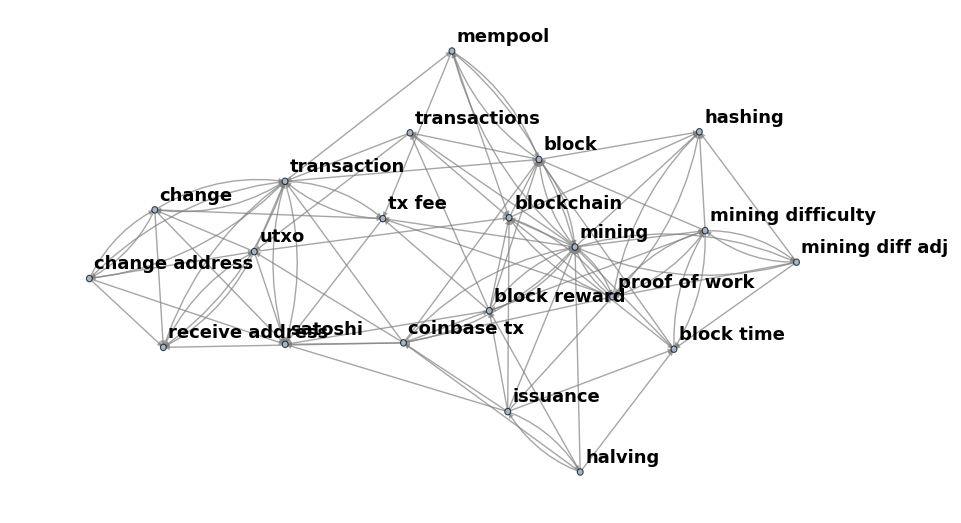

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
twoD=Graph[
literals
,VertexSize->Small
,VertexLabels->"Name"
,VertexLabelStyle->Directive[Black,18, Bold]
,EdgeStyle->Directive[Gray]
,EdgeShapeFunction->{{"CarvedArrow","ArrowSize"->.02}}
]
```

```mathematica
threeD=Graph3D[
literals
,Boxed->True
,BoxStyle->Directive[Dashed]
,VertexLabels->"Name"
,VertexLabelStyle->Directive[Red,18, Bold]
, VertexSize->0.2
,VertexStyle->Orange
, EdgeStyle->Directive[Thick]
,EdgeShapeFunction->{{"CarvedArrow","ArrowSize"->.02}}
]
```

-Graphics3D-

## Community Graph

```mathematica
CommunityGraphPlot[
literals
,ImageSize-> 900
,ImageMargins->20
,VertexSize->0.05
, VertexLabels->"Name"
,CommunityBoundaryStyle->Automatic
,VertexLabelStyle->Directive[Red,Italic,Bold,15]
(*,EdgeShapeFunction->{{"CarvedArrow","ArrowSize"->.01}}*)
]
```

-Graphics-

## Layered Graph

```mathematica
LayeredGraphPlot[
literals
,Bottom
,ImageSize-> 1200
,ImageMargins->20
,VertexSize->{2.75,.5}
, AspectRatio->1
,VertexLabelStyle->Directive[Bold,15]
(*,VertexSize->0.05
, VertexLabels->"Name"
,EdgeShapeFunction->{{"CarvedArrow","ArrowSize"->.02}}
*)
, PlotTheme->"ClassicDiagram"
]
```

-Graphics-

```mathematica
ReverseSortBy[Table[{vertices[[x]],VertexDegree[literals][[x]]},{x,1,Length[vertices]}],Last]
```

{{mining,20},{transaction,15},{proof of work,12},{block,12},{coinbase tx,11},{block reward,11},{blockchain,11},{mining difficulty,10},{utxo,9},{satoshi,9},{issuance,9},{tx fee,8},{change,8},{block time,8},{receive address,7},{mining diff adj,7},{mempool,7},{hashing,7},{change address,7},{transactions,6},{halving,6}}

## Scoring prerequisites and complexities

### Prerequisites Scores

```mathematica
prerequisites =AssociationThread@@(ReverseSortBy[
Table[{
vertices[[x]]
,VertexInDegree[literals][[x]]}
,{x,1,Length[vertices]
}]
,Last]
//Transpose
);
prerequisites//Dataset[
#
,ItemStyle->{Black}
,HeaderStyle->Bold
, HeaderBackground->LightYellow
, MaxItems->(vertices//Length)
]&
```

### Complexity Scores

```mathematica
complexity=AssociationThread@@(ReverseSortBy[
Table[{
vertices[[x]]
, VertexOutDegree[literals][[x]]}
, {x, 1, Length[vertices]}]
, Last
]
//Transpose
);
complexity//Dataset[#,ItemStyle->{Black},HeaderStyle->Bold, HeaderBackground->LightYellow, MaxItems->(vertices//Length)]&
```

### Prerequisite minus Complexity Scores

```mathematica
ReverseSort[Merge[{prerequisites,-complexity},Total]]//Dataset[#,ItemStyle->{Black},HeaderStyle->Bold, HeaderBackground->LightYellow, MaxItems->(vertices//Length)]&
```

## Vertex views

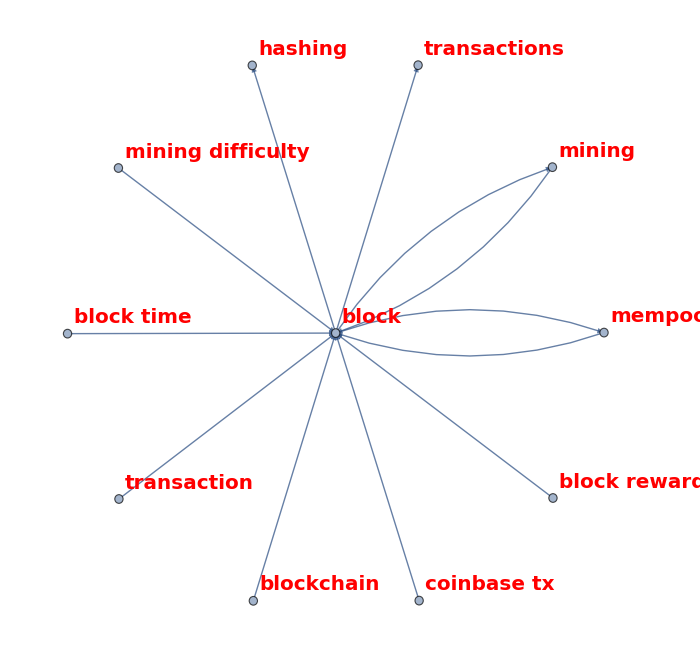
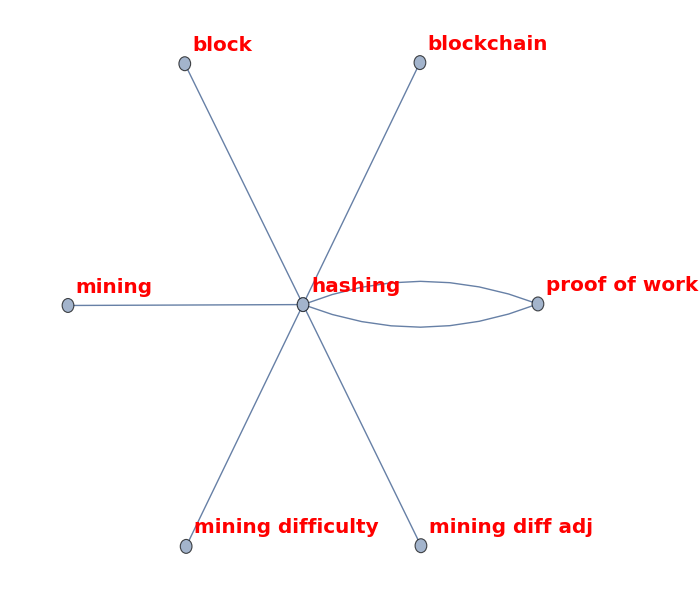
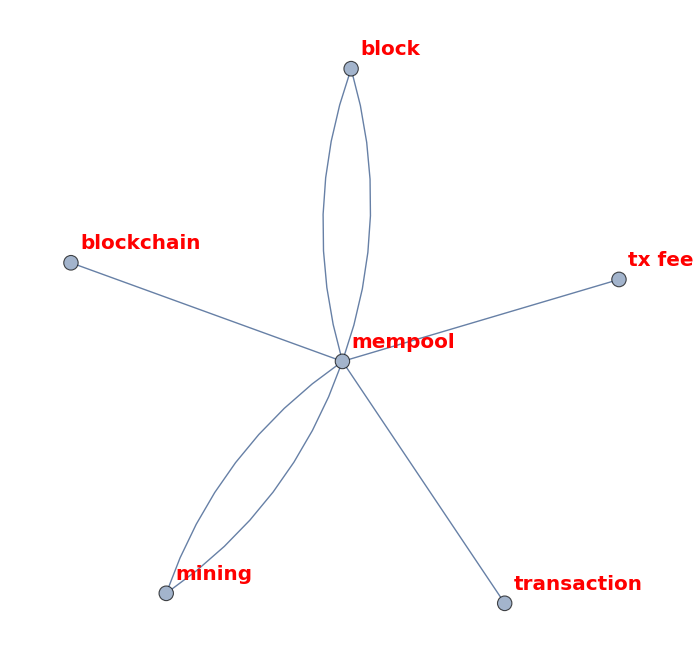
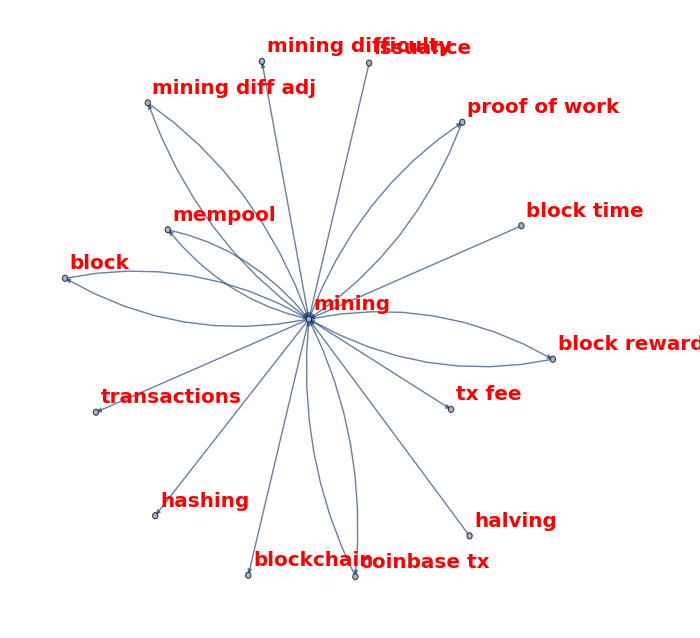
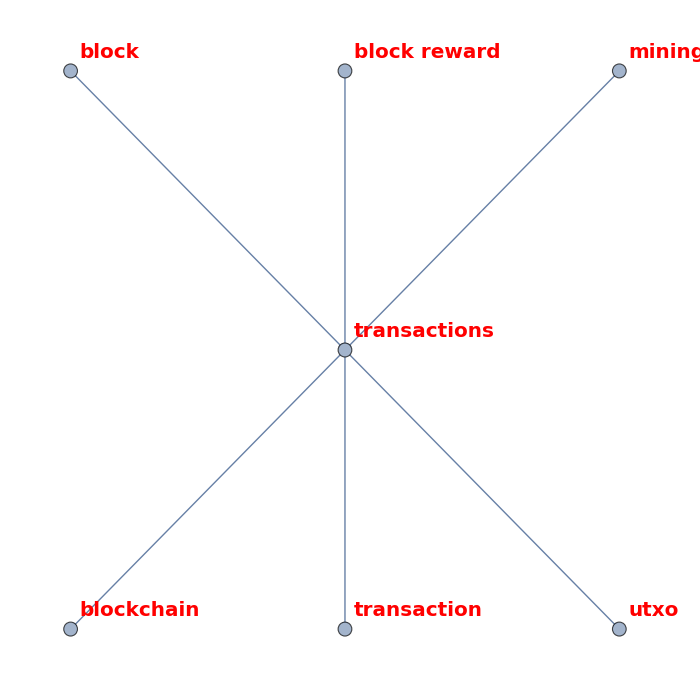
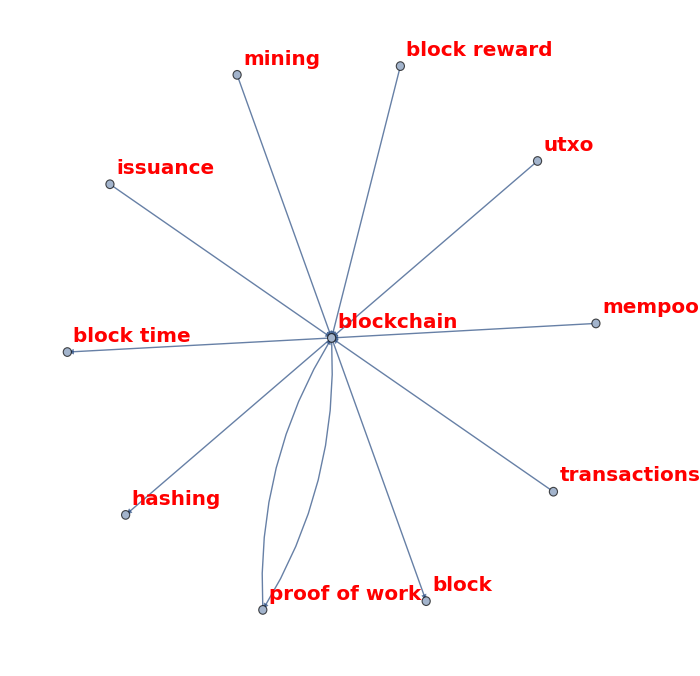
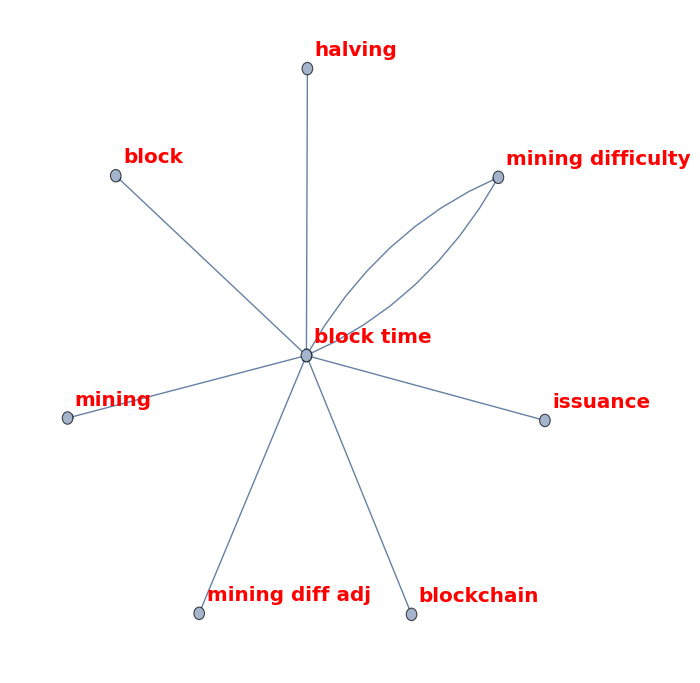
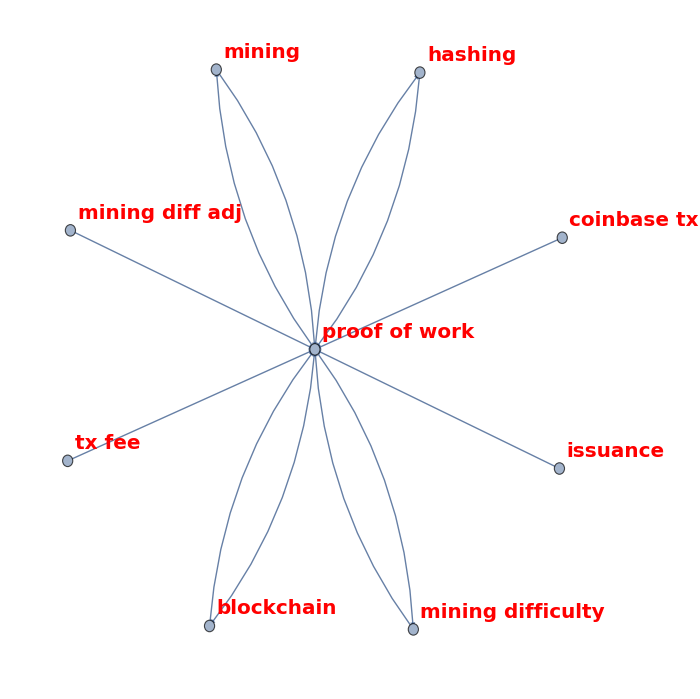
{-Graphics-block,-Graphics-hashing,-Graphics-mempool,-Graphics-mining,-Graphics-transactions,-Graphics-blockchain,-Graphics-block time,-Graphics-proof of work,-Graphics-block reward,-Graphics-mining difficulty,-Graphics-satoshi,-Graphics-tx fee,-Graphics-change,-Graphics-change address,-Graphics-receive address,-Graphics-transaction,-Graphics-utxo,-Graphics-coinbase tx,-Graphics-halving,-Graphics-issuance,-Graphics-mining diff adj}

```mathematica
Table[
Labeled[
Framed[
Graph[
Select[literals,#[[1]]==x || #[[2]]==x&]
(*,ImageSize-> 700*)
,ImageMargins->20
,VertexSize->0.05
, VertexLabels->"Name"
,VertexLabelStyle->Directive[Red,Italic,Bold,20]
,EdgeShapeFunction->{{"CarvedArrow","ArrowSize"->.02}}
]
]
,x
,Top
,LabelStyle->"Section"
]
,{x,vertices}
]
```

```mathematica
literals//Length
```

100

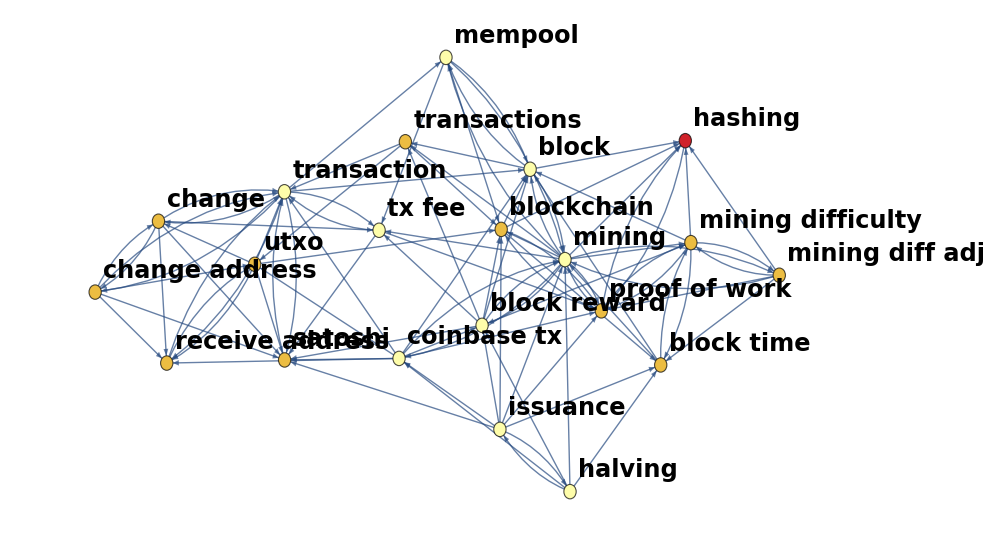

```mathematica
ve=Table[VertexEccentricity[literals,v],{v,vertices}];
HighlightGraph[literals,Table[Style[v,ColorData["TemperatureMap",ve⟦VertexIndex[literals,v]⟧/Max[ve]]],{v,vertices}],VertexLabels->"Name",VertexLabelStyle->Directive[Black,24, Bold]]
```

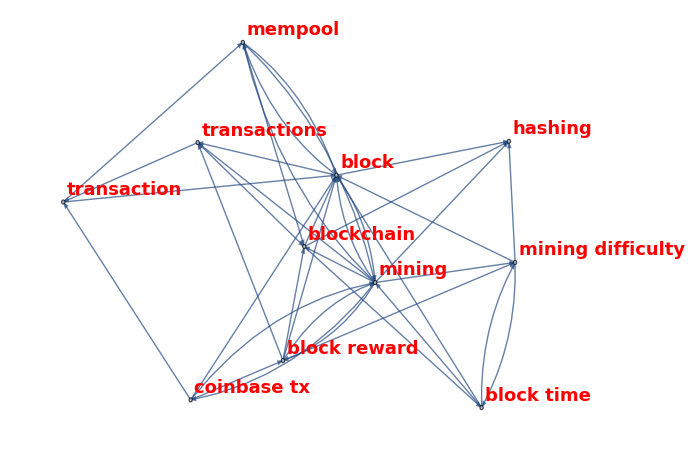
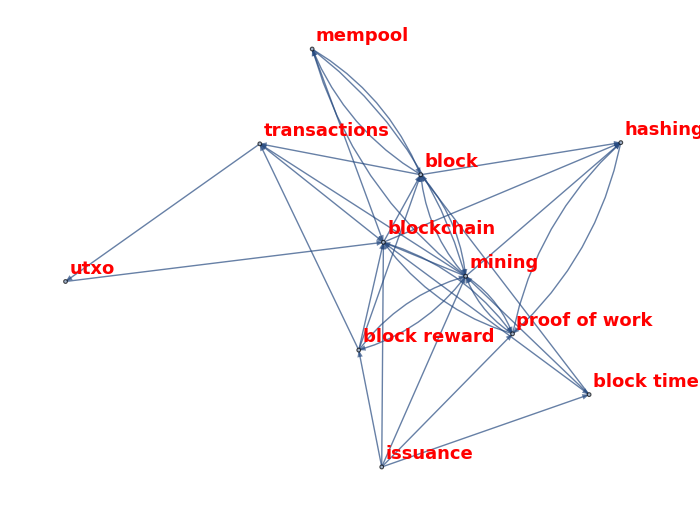
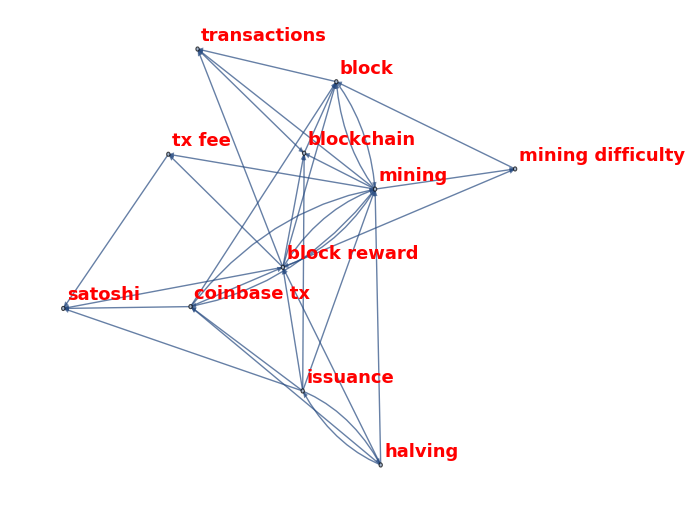
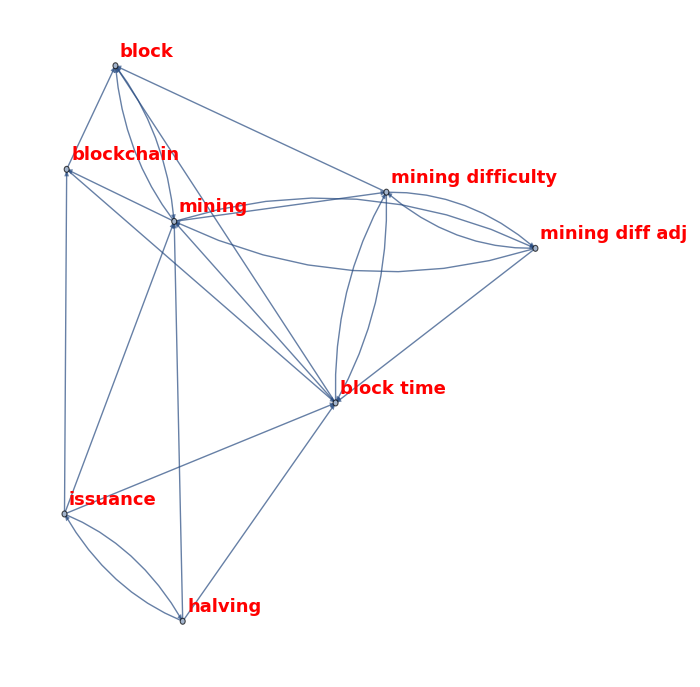
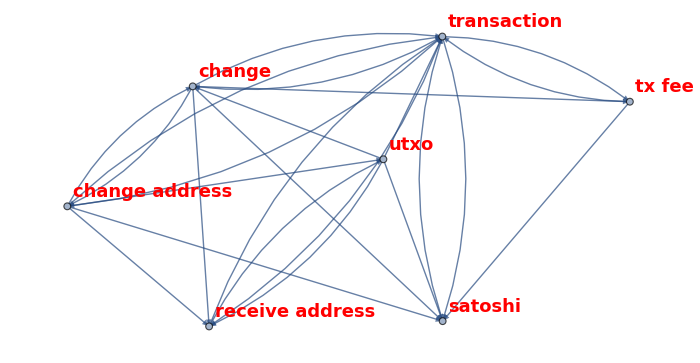
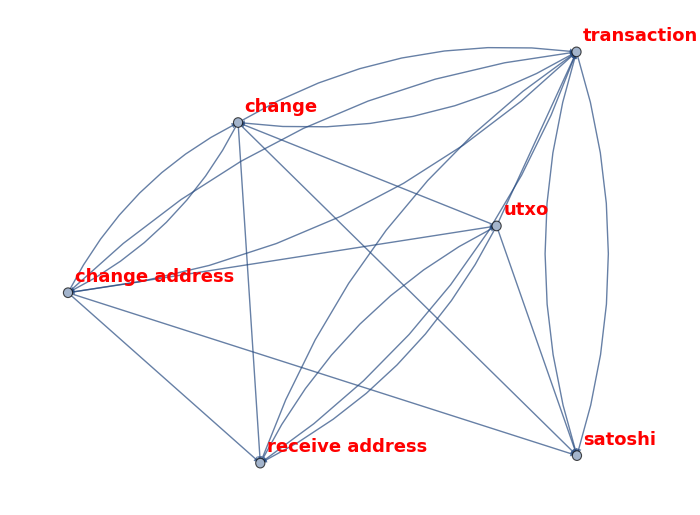
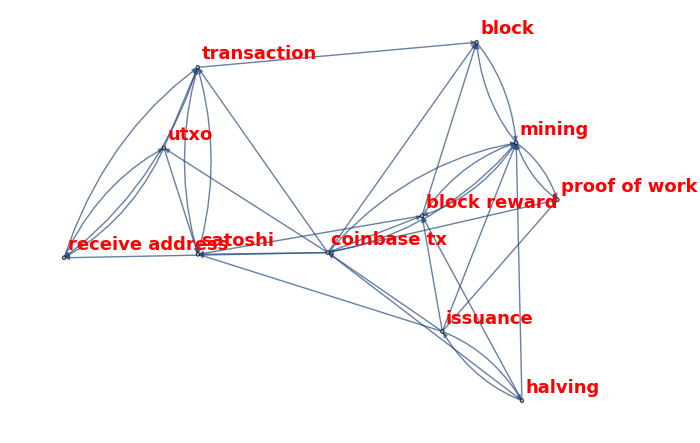
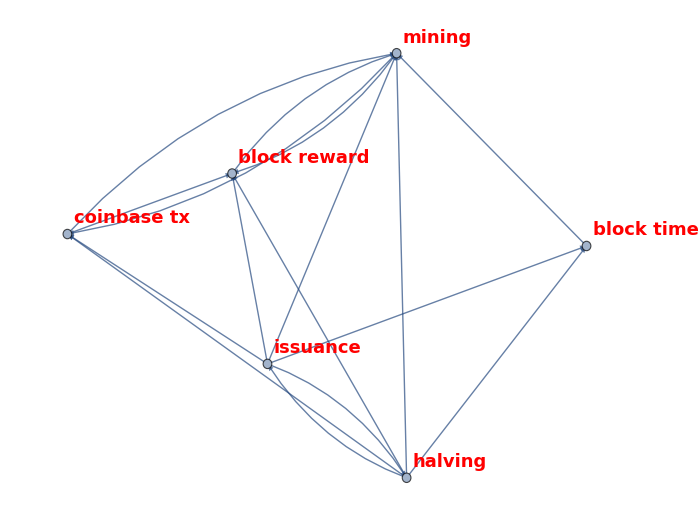
{-Graphics-block neighborhood,-Graphics-blockchain neighborhood,-Graphics-block reward neighborhood,-Graphics-block time neighborhood,-Graphics-change neighborhood,-Graphics-change address neighborhood,-Graphics-coinbase tx neighborhood,-Graphics-halving neighborhood,-Graphics-hashing neighborhood,-Graphics-issuance neighborhood,-Graphics-mempool neighborhood,-Graphics-mining neighborhood,-Graphics-mining diff adj neighborhood,-Graphics-mining difficulty neighborhood,-Graphics-proof of work neighborhood,-Graphics-receive address neighborhood,-Graphics-satoshi neighborhood,-Graphics-transaction neighborhood,-Graphics-transactions neighborhood,-Graphics-tx fee neighborhood,-Graphics-utxo neighborhood}

```mathematica
Table[
Labeled[
Framed[
NeighborhoodGraph[
literals
,x
,ImageSize-> 700
,ImageMargins->20
,VertexSize->0.05
, VertexLabels->"Name"
,VertexLabelStyle->Directive[Red,Italic,Bold,18]
,EdgeShapeFunction->{{"CarvedArrow","ArrowSize"->.02}}
]
]
,StringJoin[x,  " neighborhood"]
,Top
,LabelStyle->"Section"
]
,{x,vertices//Sort}
]
```

```mathematica
AssociationThread[VertexList[literals],VertexDegree[literals]]//ReverseSort
```

<|mining→20,transaction→15,proof of work→12,block→12,coinbase tx→11,block reward→11,blockchain→11,mining difficulty→10,issuance→9,utxo→9,satoshi→9,change→8,tx fee→8,block time→8,mining diff adj→7,receive address→7,change address→7,mempool→7,hashing→7,halving→6,transactions→6|>

```mathematica
LayeredGraphPlot[
literals
,Bottom
,ImageSize-> 900
,ImageMargins->20
,VertexSize->{2.75,.5}
, AspectRatio->0.75
,VertexLabelStyle->Directive[Bold,15]
(*,VertexSize->0.05
, VertexLabels->"Name"
,EdgeShapeFunction->{{"CarvedArrow","ArrowSize"->.02}}
*)
, PlotTheme->"ClassicDiagram"
]
```

-Graphics-